{{y→InterpolatingFunction[{{0., 10.}}, <>]}}

DSolve[{-y'[n]^2+1. y[n] y''[n]+y^(3)[n]==0,y[0]==0,y'[0]==1,y'[10]==0},y,{n,0,10}]

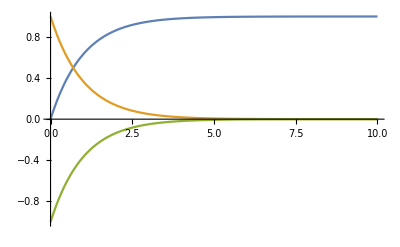

{{{0.,-1.00001}},{{0.001,-0.997083}}}

{{InterpolatingFunction[{{0., 10.}}, <>][n]}}

```mathematica
l = 1;
s=NDSolve[{y'''[n]+0.5*(1+l)y[n]y''[n]-l y'[n]^2==0,
y[0]==0,y'[0]==1, y'[10]==0},
y,
{n,0,10}]
Plot[Evaluate[{y[n],y'[n], y''[n]}/.s],{n,0,10},PlotStyle->Automatic]

Table[{n,y''[n]}/.s,{n,0,0.001,0.001}]
```

```mathematica
y/.s
```

{InterpolatingFunction[{{0., 10.}}, <>]}

```mathematica
Clearall
```

Clearall

```mathematica
sol=DSolve[{y'''[n]+0.5*(1+l)y[n]y''[n]-l y'[n]^2==0,
y[0]==0,y'[0]==1, y'[10]==0},
y,
{n,0,10}]
```

DSolve[{-y'[n]^2+1. y[n] y''[n]+y^(3)[n]==0,y[0]==0,y'[0]==1,y'[10]==0},y,{n,0,10}]